Linear Combination of Unitaries |

General Implementationpaclet:Q3/tutorial/LinearCombinationofUnitaries#221637712 | Examplespaclet:Q3/tutorial/LinearCombinationofUnitaries#2113806542

UniformlyControlledGatepaclet:Q3/ref/UniformlyControlledGateQ3 Package Symbol | Uniformly controlled unitary gates

Q3 functions that are useful to construct a linear combination of unitaries.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

General Implementation

Let U_1,U_2,… be unitary operators. and α:=(α_1,α_2,…) be a vector of complex numbers. Define a unitary operator Vby

V≐1/(√(‖α‖_1))(√α_1 | * | … | *
√α_2 | * | … | *
⋮ | ⋮ | ⋱ | ⋮
⋮ | * | … | *) .

Then, one way to implement T:=∑_k α_k U_k is through the quantum circuit in Figure 1.

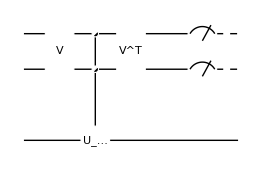
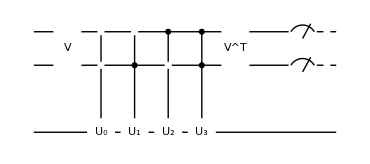
-Graphics-=-Graphics-

Figure 1. A quantum circuit implementing the linear combination of unitary gates, ∑_k α_k U_k. Here, Here, V^T is a unitary operator the matrix representation of which is given by the transpose of that of V in the computational basis.

Examples

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,A,S]
Let[Complex,c]
```

Consider a system register consisting of n qubits.

```mathematica
$n=1;
SS=S[Range@$n,$]
```

{S_(,,1)}

Take some unitary gates U_k (k=0,…,2^m-1) on the system register.

```mathematica
$m=2;
```

```mathematica
U[k_]:=Rotation[Pi*k/6,S[1,2]]
UU=Table[U[k],{k,Range@Power[2,$m]-1}]
```

{Exp(0),Exp(-1/12 ⅈ π S_(,,1)^(,,Y)),Exp(-1/6 ⅈ π S_(,,1)^(,,Y)),Exp(-1/4 ⅈ π S_(,,1)^(,,Y))}

We will need an ancilla register of m qubits.

```mathematica
AA=A[Range@$m,$]
```

{A_(,,1),A_(,,2)}

### Simple Sum

Consider the sum T:=∑_k U_k of the unitary gates.

```mathematica
TT=Sum[U[k],{k,0,3}]
```

Exp(0)+Exp(-1/12 ⅈ π S_(,,1)^(,,Y))+Exp(-1/6 ⅈ π S_(,,1)^(,,Y))+Exp(-1/4 ⅈ π S_(,,1)^(,,Y))

In general, T is not unitary, and cannot be directly implemented on a quantum computer. However, one can realize it probabilistically with a quantum circuit of the form and post-selection with respect to the ancilla register for state 00…0.

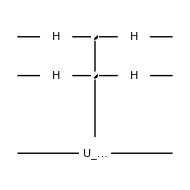

```mathematica
qc=QuantumCircuit[
Ket[AA],
Through[AA[6]],
UniformlyControlledGate[AA,UU,"Label"->"U"],
Through[AA[6]],
"Invisible"->A[$m+1/2]
]
```

The above quantum circuit is, of course, equivalent to the following one.

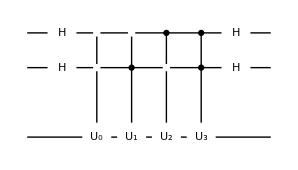

```mathematica
Expand[qc]
```

To test  it, take an arbitrary input state.

```mathematica
in=ProductState[S[1]->c@{0,1},"Label"->Ket@{"ψ"}]
```

(c_(,,0) 0+c_(,,1) 1)_(S_(,,1))

```mathematica
full=QuantumCircuit[in,qc]
```

-Graphics-

Take the projection operator onto 00…0.

```mathematica
prj=Dyad[Ket[AA],Ket[AA],AA]
```

0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,1))0_(,,A_(,,2))

```mathematica
out=prj**full
out=KetCanonical@KetDrop[out,AA]
```

1/16 ((4+3 √2+2 √3+√6) c_(,,0)-(2+√2+√6) c_(,,1)) 0_(,,A_(,,1))0_(,,A_(,,2))0_(,,S_(,,1))+1/16 ((2+√2+√6) c_(,,0)+(4+3 √2+2 √3+√6) c_(,,1)) 0_(,,A_(,,1))0_(,,A_(,,2))1_(,,S_(,,1))

0_(,,S_(,,1))+(((2+√2+√6) c_(,,0)+(4+3 √2+2 √3+√6) c_(,,1)) 1_(,,S_(,,1)))/((4+3 √2+2 √3+√6) c_(,,0)-(2+√2+√6) c_(,,1))

Compare the above result with the direct operation of T on the input state.

```mathematica
new=Elaborate@KetCanonical[T**in]
```

0_(,,S_(,,1))+(((2+√2+√6) c_(,,0)+(4+3 √2+2 √3+√6) c_(,,1)) 1_(,,S_(,,1)))/((4+3 √2+2 √3+√6) c_(,,0)-(2+√2+√6) c_(,,1))

```mathematica
out-new
```

0

### Linear Superposition

Let us now consider a more general form of linear combination T:=∑_k α_k U_k of the unitary gates.

```mathematica
α={1,1/2,-I,-I/2}
```

{1,1/2,-ⅈ,-ⅈ/2}

```mathematica
TT=α.UU
```

Exp(0)+1/2 (Exp(-1/12 ⅈ π S_(,,1)^(,,Y)))-ⅈ (Exp(-1/6 ⅈ π S_(,,1)^(,,Y)))-1/2 ⅈ (Exp(-1/4 ⅈ π S_(,,1)^(,,Y)))

We fist construct the so-called preparation oracles, V and V^T

```mathematica
matV=Normal@One[Power[2,$m]];
matV[[1]]=Sqrt[N@α]/Norm[α,1];
matV=Transpose[Chop@Orthogonalize@matV];
matV//MatrixForm
```

(0.57735 | -0.258199 | -0.365148-0.365148 ⅈ | -0.408248-0.408248 ⅈ
0.408248 | 0.912871 | 0 | 0
0.408248-0.408248 ⅈ | -0.182574+0.182574 ⅈ | 0.774597 | 0
0.288675-0.288675 ⅈ | -0.129099+0.129099 ⅈ | -0.365148 | 0.816497)

```mathematica
matV.Topple[matV]//Chop//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
VV=Operator[matV,AA,"Label"->"V"]
VT=Operator[Transpose@matV,AA,"Label"->"V^T"]
```

Operator[…]

Operator[…]

Construct the so-called selection oracle, W, which is just given by the uniformly-controlled gate.

```mathematica
WW=UniformlyControlledGate[AA,UU,"Label"->"U"]
```

UniformlyControlledGate[{A_(,,1),A_(,,2)},{Exp(0),Exp(-1/12 ⅈ π S_(,,1)^(,,Y)),Exp(-1/6 ⅈ π S_(,,1)^(,,Y)),Exp(-1/4 ⅈ π S_(,,1)^(,,Y))},Label→U]

Take the overall quantum circuit.

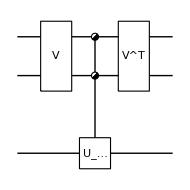
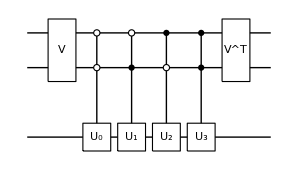
-Graphics-=-Graphics-

```mathematica
qc=QuantumCircuit[
Ket[AA],in,
VV,WW,VT,
"Invisible"->A@{$m+1/2}
];
Row@{qc,"=",Expand[qc]}
```

Calculate the output state, and perform the post-selection.

```mathematica
out=prj**qc//KetChop;
out=KetCanonical@KetDrop[out,AA]
```

0_(,,S_(,,1))+(((0.334428-0.300542 ⅈ) c_(,,0)+(1.-5.55112×10^-17 ⅈ) c_(,,1)) 1_(,,S_(,,1)))/(1. c_(,,0)-(0.334428-0.300542 ⅈ) c_(,,1))

Compare the result above with the one from directly applying T on the input state.

```mathematica
new=Elaborate@KetCanonical[TT**in]
```

0_(,,S_(,,1))+(((-4 ⅈ-(1+2 ⅈ) √2+√6) c_(,,0)+(8+(1-2 ⅈ) √2-4 ⅈ √3+√6) c_(,,1)) 1_(,,S_(,,1)))/((8+(1-2 ⅈ) √2-4 ⅈ √3+√6) c_(,,0)+(4 ⅈ+(1+2 ⅈ) √2-√6) c_(,,1))

```mathematica
out-new//Garner//Chop
```

0

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3

| Related Links
▪A. Gilyen, Y. Su, G. Hao, and N. Wiebe (2019)https://doi.org/10.1145/3313276.3316366, Proceedings of the 51st Annual ACM SIGACT Symposium on Theory of Computing, "Quantum singular value transformation and beyond: exponential improvements for quantum matrix arithmetics."
▪L. Lin (2022)https://arxiv.org/abs/2201.08309, arXiv:2201.08309, "Lecture Notes on Quantum Algorithms for Scientific Computation."
▪J. M. Martyn, Z. M. Rossi, A. K. Tan, I. L. Chuan (2021)https://doi.org/10.1103%2Fprxquantum.2.040203, PRX Quantum 2, 4 040203, "Grand Unification of Quantum Algorithms."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).